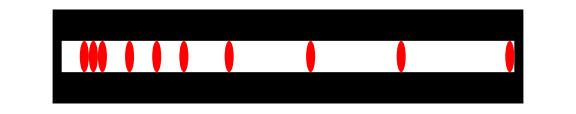

```mathematica
m =50;
n= 10;
d = RandomSample[Range[m],n];
Graphics[{
{Black, Rectangle[{0,-1},{m+2,2}]},
{White, Rectangle[{1,0},{m+1,1}]},
{Red,Table[ Disk[{d⟦i⟧+1/2,1/2},1/2],{i,n}]}
},ImageSize->Large]
```

### How hard is "Mapping, F“/Users/ab55/Desktop/git/MagneticController/MassiveUniformControl/IROS2017mapping/IdeasForPaper.tex”oraging, and Coverage with a Particle Swarm Controlled by Uniform Inputs" in 1D? The expected time to reach both boundaries is (3 (1+n))/(1+k). The smartCow movement is worse. (distributions of these are beta distributions: http://math.stackexchange.com/questions/350682/expected-value-of-distance-between-min-and-max-of-independent-events-with-unifor) We can approximate the biggest gap because the gaps are approximately beta-distributions and we want the maximum order statistic TODO: what happens if you do the ‘smart cow’ movement? Compare with and without GAPs -- gap is very important. Does it dominant the time? http://math.stackexchange.com/questions/66430/what-is-the-distribution-of-gaps Compare analytical model and MonteCarlo -- Done for reaching boundary PLOT 1: I want a plot of average number of moves for n = 1000, and k = 1:100. Easy to simulate, done PLOT 2:

```mathematica
m =5000;trials =2000;
numMovesFullCoverage5000 =Table[ (*If[Mod[n,1]==0,Print[StringForm["n=``",n]]];*)
Print[StringForm["n=``",n]];
Module[{T},T=Table[sim1Dcoverage[m,n],{trials}];
{n,Mean[T],StandardDeviation[T]}],{n,100,m,100}];
```

n=100

n=200

n=300

n=400

n=500

n=600

n=700

n=800

n=900

n=1000

n=1100

n=1200

n=1300

n=1400

n=1500

n=1600

n=1700

n=1800

n=1900

n=2000

n=2100

n=2200

n=2300

n=2400

n=2500

n=2600

n=2700

n=2800

n=2900

n=3000

n=3100

n=3200

n=3300

n=3400

n=3500

n=3600

n=3700

n=3800

n=3900

n=4000

n=4100

n=4200

n=4300

n=4400

n=4500

n=4600

n=4700

n=4800

n=4900

n=5000

```mathematica
N[numMovesFullCoverage5000]
```

{{100.,306.535,77.2571},{200.,169.889,39.2712},{300.,120.012,26.3169},{400.,93.224,19.8018},{500.,75.933,15.62},{600.,64.51,12.6483},{700.,55.6065,10.6329},{800.,49.4255,9.11674},{900.,44.3765,8.26286},{1000.,39.8965,6.99122},{1100.,36.549,6.56263},{1200.,33.6495,5.91736},{1300.,31.117,5.42162},{1400.,28.677,4.70656},{1500.,26.9615,4.41404},{1600.,25.2435,4.14871},{1700.,23.631,3.7769},{1800.,22.373,3.67119},{1900.,21.106,3.43783},{2000.,20.099,3.18061},{2100.,19.0235,2.98637},{2200.,18.1465,2.84308},{2300.,17.225,2.6427},{2400.,16.3445,2.5393},{2500.,15.5695,2.32031},{2600.,14.919,2.22011},{2700.,14.2845,2.1028},{2800.,13.662,2.01539},{2900.,13.114,1.84816},{3000.,12.533,1.82115},{3100.,12.013,1.63376},{3200.,11.496,1.57201},{3300.,11.051,1.46952},{3400.,10.6985,1.41301},{3500.,10.1755,1.33626},{3600.,9.7675,1.28774},{3700.,9.4025,1.22729},{3800.,8.9765,1.14569},{3900.,8.6335,1.12642},{4000.,8.282,1.0247},{4100.,7.892,0.937964},{4200.,7.5625,0.899721},{4300.,7.215,0.814928},{4400.,6.8755,0.826039},{4500.,6.5065,0.687891},{4600.,6.191,0.62906},{4700.,5.7675,0.640038},{4800.,5.3345,0.534558},{4900.,4.908,0.421456},{5000.,2.,0.}}

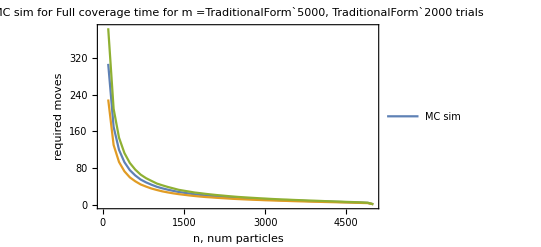

```mathematica
p1 = ListLinePlot[{Transpose[{numMovesFullCoverage5000⟦;;,1⟧,numMovesFullCoverage5000⟦;;,2⟧}],
Transpose[{numMovesFullCoverage5000⟦;;,1⟧,numMovesFullCoverage5000⟦;;,2⟧-numMovesFullCoverage5000⟦;;,3⟧}],
Transpose[{numMovesFullCoverage5000⟦;;,1⟧,numMovesFullCoverage5000⟦;;,2⟧+numMovesFullCoverage5000⟦;;,3⟧}]
}
,Joined->True,(*Mesh->All,*)Filling->2->3,(*PlotLegends->{"Min","Max","Diff"},*)PlotLabel->StringForm["MC sim for Full coverage time for m =``, `` trials",m, trials],PlotRange->All,
Frame->{True,True,False,False},PlotLegends->{"MC sim"},
FrameLabel->{"n, num particles","required moves"}
]
```

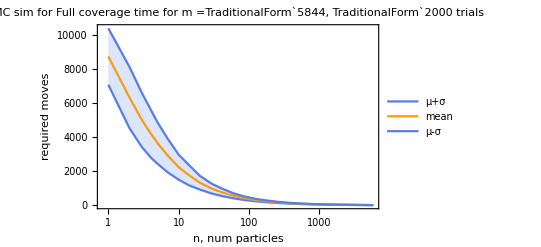

```mathematica
p1 = ListLogLinearPlot[{
Transpose[{numMovesFullCoverage5844⟦;;,1⟧,numMovesFullCoverage5844⟦;;,2⟧-numMovesFullCoverage5844⟦;;,3⟧}],
Transpose[{numMovesFullCoverage5844⟦;;,1⟧,numMovesFullCoverage5844⟦;;,2⟧}],
Transpose[{numMovesFullCoverage5844⟦;;,1⟧,numMovesFullCoverage5844⟦;;,2⟧+numMovesFullCoverage5844⟦;;,3⟧}]
}
,PlotStyle->{-Graphics-,-Graphics-,-Graphics-},Joined->True,(*Mesh->All,*)Filling->{1->{ 3}},(*PlotLegends->{"Min","Max","Diff"},*)PlotLabel->StringForm["MC sim for Full coverage time for m =``, `` trials",m, trials],PlotRange->All,
Frame->{True,True,False,False},PlotLegends->Placed[{"μ+σ","mean","μ-σ"},Center],
FrameLabel->{"n, num particles","required moves"}
]
```

```mathematica
m =1000;
numMovesFullCoverage1000 =Table[ If[Mod[n,1]==0,Print[StringForm["n=``",n]]];{n,Mean[Table[sim1Dcoverage[m,n],{2000}]]},{n,Ceiling[PowerRange[1,500,1.45]]}];
```

n=1

n=2

n=3

n=4

n=5

n=7

n=10

n=14

n=20

n=29

n=42

n=60

n=87

n=126

n=182

n=264

n=382

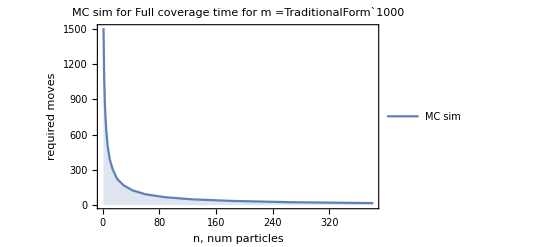

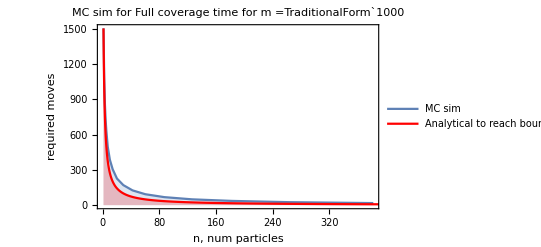

```mathematica
p1 = ListLinePlot[numMovesFullCoverage1000,Filling->Axis,(*PlotLegends->{"Min","Max","Diff"},*)PlotLabel->StringForm["MC sim for Full coverage time for m =``",m],PlotRange->All,
Frame->{True,True,False,False},PlotLegends->{"MC sim"},
FrameLabel->{"n, num particles","required moves"}
]

pg = Plot[coverEndpoints[m,n],{n,1,512},PlotStyle->Red,Filling->Axis,PlotRange->All,
(*Frame->{True,True,False,False},*)
AxesLabel->{"n, num particles","required moves"},PlotLegends->{"Analytical to reach boundaries"},
PlotLabel->StringForm["Find boundaries: m = ``",m]];
Show[p1,pg]
```

```mathematica
m
```

1000

### Draw without replacement n times from [0,...,m]

```mathematica
m=1000;
n=10;trials=1000000;
mAndM = Table[d=RandomSample[Range[m],n];{Min[d],Max[Differences[Sort[Join[d,{0,m+1}]]]],Max[d]-Min[d],Max[d]},{trials}];
SmoothHistogram[Transpose[mAndM],Filling->Axis,PlotLegends->Placed[{"p̲","ḡ","p̄-p̲","p̄"},{Top,Center}],AxesLabel->{"m","Prob"},PlotLabel->StringForm["m=``, n=``, `` trials",m,n,trials],PlotRange->All]
```

-Graphics-

```mathematica
N[Mean[mAndM]]
```

{90.9362,273.942,819.086,910.023}

```mathematica
1001-910.022601
```

90.9774

## Simulate 1D coverage with particles controlled by uniform inputs

```mathematica
sim1Dcoverage[m_,n_]:=Module[{ds,mg},
(* Returns the total number of moves to cover the space and find the boundaries.
First, select n points from m positions,
then sort the points.  Find the min=ds⟦1⟧ and max=ds⟦-1⟧ and the max gap = mg.
To cover, move to the left ds⟦1⟧ moves.  The left robot has hit the left boundary. 
If there exists a gap from left to right robot at start (i.e. ds⟦1⟧ = m-n+1), the right robot started at ds⟦-1⟧,   and moved left  ds⟦1⟧.  It then must move right ds⟦1⟧+m-ds⟦-1⟧ + 1 moves.

If no gaps from left to right robot at start, the right robot started at ds⟦-1⟧, and moved left  ds⟦1⟧-1.  It then must move right ds⟦1⟧+m-ds⟦-1⟧ moves. This has probability (m-n+1)/Binomial[m,n]  because there are m-n gaps that can be placed on either side of the clump of robots (m-n+1 possible clumpings), so we will skip it in simulation.
Covering the gaps requires extra moves
 *)
ds = Sort[RandomSample[Range[m],n]];
mg = Max[Differences[ds]];
Return[
2*ds⟦1⟧
+m-ds⟦-1⟧ +If[n<m,1,0]+ Max[mg-(ds⟦1⟧+m-ds⟦-1⟧ ),0 ]]
]
sim1DcoverageVars[m_,n_]:=Module[{ds,mg},
(* Returns the total number of moves to cover the space and find the boundaries,
total number of moves to cover the space and find the boundaries,
and the maximum interior gap.
 *)
ds = Sort[RandomSample[Range[m],n]];
mg = Max[Differences[ds]];
Return[{
2*ds⟦1⟧+m-ds⟦-1⟧ +1+ Max[mg-(ds⟦1⟧+m-ds⟦-1⟧ ),0 ],
2*ds⟦1⟧+m-ds⟦-1⟧ +1,
mg}]
]

sim1DcoverageMinMax[m_,n_]:=Module[{ds},
(* Returns the total number of moves to cover the space
First, select n points from m positions
then sort the points.  Find the min and max 
 *)
ds = Sort[RandomSample[Range[m],n]];
Return[2*ds⟦1⟧+m-ds⟦-1⟧ +1]
]

sim1DcoverageMinMaxSmartCow[n_,k_]:=Module[{d,ds,success,pos,mv,totalmv},
(* Returns the total number of moves to cover the space
First, select k points from N positions
then sort the points.  Find the min and max and the max gap
 *)
d=RandomSample[Range[n],k];
ds = Sort[d];
(* move left 1, right 2, left 4 etc.*)
success = False;
pos = 0;
mv = 1;
totalmv = 0;
(*Print[{ds⟦1⟧,ds⟦-1⟧,pos,mv}];*)
While[!success&& Abs[mv]<10000,
(*Print[{ds⟦1⟧,ds⟦-1⟧,pos,mv}];*)
If[ ds⟦1⟧ ≤pos-mv,
success = True; totalmv += ds⟦1⟧+pos + ds⟦1⟧+n-ds⟦-1⟧, 
pos-=mv;totalmv +=mv;mv *=2;
(*Print[{ds⟦1⟧,ds⟦-1⟧,pos,mv}];*)
If[ n-ds⟦-1⟧≤pos+mv,
success = True; totalmv +=n- ds⟦-1⟧-pos +n-ds⟦-1⟧+ds⟦1⟧,
pos+=mv;totalmv +=mv;mv *=2;]]
];
Return[totalmv]
]
```

```mathematica
sCsim1000p10 = Table[sim1DcoverageMinMaxSmartCow[1000,10],{1000}];
```

```mathematica
N[Mean[sCsim1000p10]]
N[Mean[mmsim1000p10]]
```

638.783

272.512

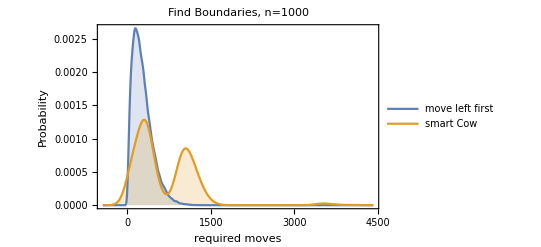

```mathematica
SmoothHistogram[{mmsim1000p10,sCsim1000p10},Filling->Axis,PlotLegends->{"move left first","smart Cow"},
Frame->{True,True,False,False},
FrameLabel->{"required moves","Probability"},
PlotLabel->"Find Boundaries, n=1000",PlotRange->All]
```

```mathematica
trials = 100000;
m=1000;
sim1000p1 = Table[sim1Dcoverage[m,1],{trials}];
sim1000p10 = Table[sim1Dcoverage[m,10],{trials}];
sim1000p100 = Table[sim1Dcoverage[m,100],{trials}];
```

```mathematica
mmsim1000p1 = Table[sim1DcoverageMinMax[m,1],{trials}];
mmsim1000p10 = Table[sim1DcoverageMinMax[m,10],{trials}];
mmsim1000p100 = Table[sim1DcoverageMinMax[m,100],{trials}];
```

```mathematica
SmoothHistogram[{sim1000p1,sim1000p10,sim1000p100},Filling->Axis,
Frame->{True,True,False,False},
FrameLabel->{"required moves","Probability"},
PlotLabel->"Full Coverage, m=1000",PlotRange->All,
PlotLegends->Placed[{"n=1","n=10","n=100"},{Top,Center}]
]
```

-Graphics-

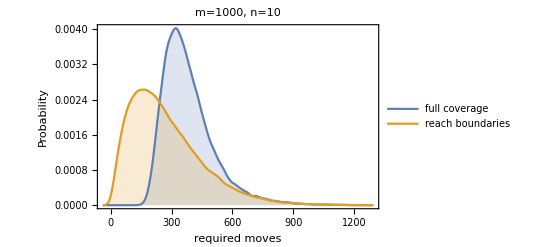

```mathematica
SmoothHistogram[{sim1000p10,mmsim1000p10},Filling->Axis,PlotLegends->{"full coverage","reach boundaries"},
Frame->{True,True,False,False},
FrameLabel->{"required moves","Probability"},
PlotLabel->"m=1000, n=10",PlotRange->All,
]
```

```mathematica
N[Mean[Transpose[{sim1000p100,mmsim1000p100}]]]
SmoothHistogram[{sim1000p100,mmsim1000p100},Filling->Axis,
Frame->{True,True,False,False},
FrameLabel->{"required moves","Probability"},
PlotLabel->"m=1000, n=100",PlotRange->All,PlotLegends->Placed[{"full coverage","reach boundaries"},{Top,Center}]]
```

{60.7284,29.8279}

-Graphics-

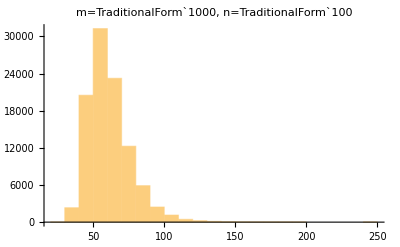

```mathematica
Histogram[sim1000p100,PlotLabel->StringForm["m=``, n=``",m,100],PlotRange->All]
```

### These plots show that the total time is a function of the maximum gap and the time to reach boundaries

```mathematica
sim1000p100var = Table[sim1DcoverageVars[1000,100],{100000}];
```

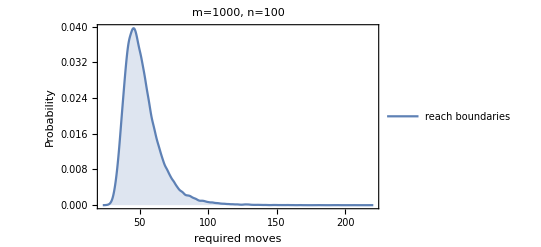

```mathematica
SmoothHistogram[Max/@Transpose[{sim1000p100var⟦;;,2⟧,sim1000p100var⟦;;,3⟧}],Filling->Axis,PlotLegends->{"reach boundaries","cover gap","total","cover boundaries + gap"},
Frame->{True,True,False,False},
FrameLabel->{"required moves","Probability"},
PlotLabel->"m=1000, n=100",PlotRange->All]
```

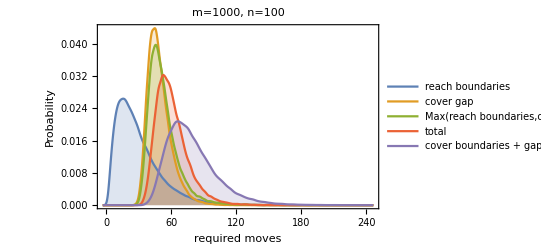

```mathematica
SmoothHistogram[{sim1000p100var⟦;;,2⟧,sim1000p100var⟦;;,3⟧,
Max/@Transpose[{sim1000p100var⟦;;,2⟧,sim1000p100var⟦;;,3⟧}],sim1000p100var⟦;;,1⟧,sim1000p100var⟦;;,3⟧+sim1000p100var⟦;;,2⟧},Filling->Axis,PlotLegends->{"reach boundaries","cover gap","Max(reach boundaries,cover gap)","total","cover boundaries + gap"},
Frame->{True,True,False,False},
FrameLabel->{"required moves","Probability"},
PlotLabel->"m=1000, n=100",PlotRange->All]
```

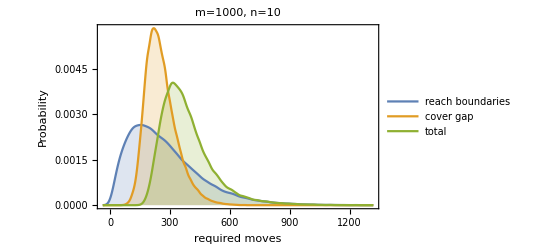

```mathematica
sim1000p10var = Table[sim1DcoverageVars[1000,10],{100000}];
SmoothHistogram[{sim1000p10var⟦;;,2⟧,sim1000p10var⟦;;,3⟧,sim1000p10var⟦;;,1⟧},Filling->Axis,PlotLegends->{"reach boundaries","cover gap","total"},
Frame->{True,True,False,False},
FrameLabel->{"required moves","Probability"},
PlotLabel->"m=1000, n=10",PlotRange->All]
```

### Expected Value to Reach left Endpoint

```mathematica
Clear[m,n,k,s,g]
FullSimplify[(*m possible locations, n robots, s is minimum position, g is maximum position.  Summation of all possible max and min positions*)
1/Binomial[m,n]∑_(s=1)^(m-n+1) Binomial[m-s-1,n-1]  s]
```

(m-n)/(1+n)

### Expected Value to Reach right Endpoint

```mathematica
Clear[m,n,k,s,g]
FullSimplify[(*m possible locations, n robots, s is minimum position, g is maximum position.  Summation of all possible max and min positions*)
1/Binomial[m,n]∑_(g=n)^m Binomial[g-1,n-1]  (m-g)]
```

(m-n)/(1+n)

### Expected Value to Reach Endpoints

```mathematica
Clear[m,n,k,s,g]
FullSimplify[(*m possible locations, n robots, s is minimum position, g is maximum position.  Summation of all possible max and min positions*)
1/Binomial[m,n]∑_(s=1)^(m-n+1) ∑_(g=s+n-1)^m Binomial[g-s-1,n-2]  (2 s +m-g+1)
(*If[g-s+1== n,(2 s +m-g),
 (2 s +m-g+1)] is the true value, but it doesn't simplify well.  Might be 1 move too many with probability 1/Binomial[m,n]*)]
```

(3 (1+m))/(1+n)

```mathematica
coverEndpoints[
m,n]:=(3 (1+m))/(1+n)
```

```mathematica
N[coverEndpoints[1000,999]]
```

3.003

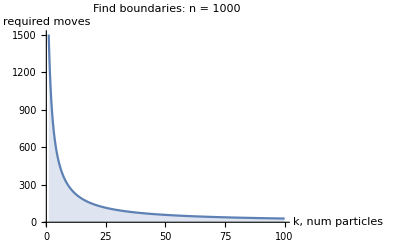

```mathematica
Plot[coverEndpoints[1000,k],{k,1,100},Filling->Axis,PlotRange->All,
(*Frame->{True,True,False,False},*)
AxesLabel->{"k, num particles","required moves"},
PlotLabel->"Find boundaries: n = 1000"]
```

How many combinations of m and M add up to (2 m + n - M + 1) = j? This is solvable as q = j-n+1, 2m +n = q, m ∈ [1,n-k+1], M ∈ [ m+k-1,n]
This is why the plot is jagged.

```mathematica
1/Binomial[n,k]∑_(m=1)^(n-k+1) ∑_(M=m+k-1)^n Binomial[M-m-1,k-2]   (2 m +n-M+1)
```

```mathematica
coverEndPointsProb[n_,k_]:=Module[{NumMoves,T,m,M},
T = 1/Binomial[n,k];
NumMoves = ConstantArray[0,2(n-k+1)+1];
For[m=1,m≤n-k+1,m++, 
For[M=m+k-1,M≤n,M++,
NumMoves⟦ 2 m +n-M+1⟧+=  T Binomial[M-m-1,k-2]
]];
Return[NumMoves]
]
```

### Compare Analytic model and Monte Carlo analysis to Reach Endpoints. The analytic model is good, but takes a long time to evaluate the full probability distribution.

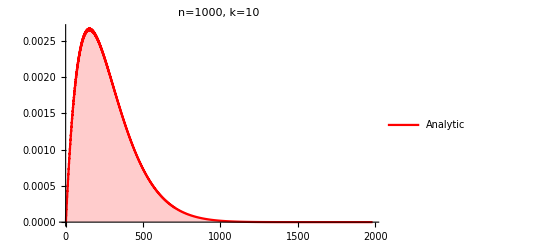

```mathematica
analytic1000k10= ListPlot[coverEndPointsProb[1000,10],PlotStyle->Red,Joined->True,Filling->Axis,PlotLegends->{"Analytic"},FrameLabel->{"required moves","Probability"},PlotLabel->"m=1000, n=10"
]
```

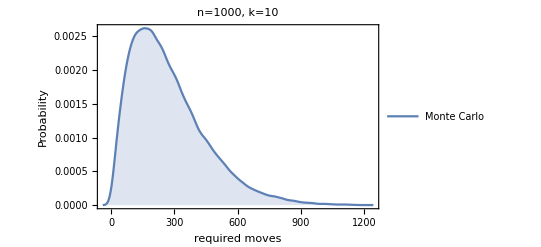

```mathematica
monteCarlo1000k10=SmoothHistogram[{sim1000p10var⟦;;,2⟧},Filling->  Axis,
PlotLegends->{"Monte Carlo"},
Frame->{True,True,False,False},
FrameLabel->{"required moves","Probability"},
PlotLabel->"n=1000, k=10",PlotRange->All]
```

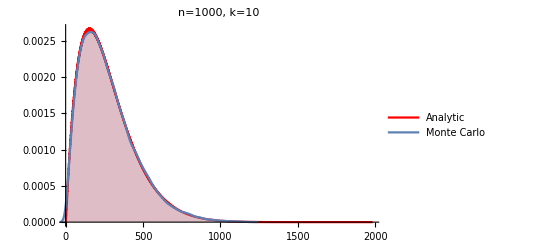

```mathematica
Show[analytic1000k10,monteCarlo1000k10]
```

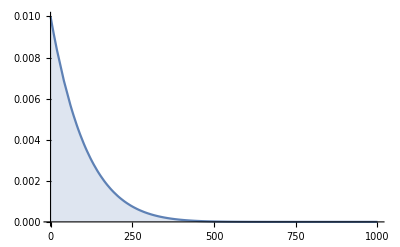

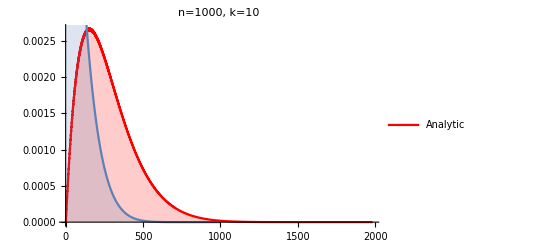

```mathematica
(*http://math.stackexchange.com/questions/459639/distribution-of-gaps-between-points?rq=1*)
beta1000k10=Plot[PDF[BetaDistribution[1,10],x/1000]/1000,{x,0,1000},Filling->Axis,PlotRange->All]
Show[analytic1000k10,beta1000k10]
```

## Try finding max gap using order statistics. see derivation at http://www.math.uah.edu/stat/sample/OrderStatistics.html

```mathematica
OrderDistribution[{UniformDistribution[],n},1]
```

BetaDistribution[1,2]

```mathematica
Clear[m,n]
mD =OrderDistribution[{BetaDistribution[1,n],n},n]
PDF[mD ,x/m]
```

OrderDistribution[{BetaDistribution[1,n],n},n]

Piecewise[{{(n (1-x/m)^(-1+n) (1-(1-x/m)^n)^(-1+n))/Beta[1,n], 0<x/m<1}, {0, True}}]

```mathematica
Piecewise[{{0, x≤0}, {(n (1-(1-x)^n)^(-1+n) (1-x)^(-1+n))/Beta[1,n], 0<x<1}, {0, True}}]
```

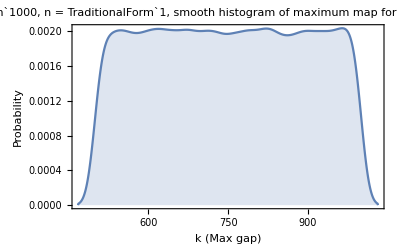

```mathematica
simMaxGap[m_,n_]:=Max[Differences[Sort[Join[RandomSample[Range[m],n],{0,m+1}]]]];
m=1000;n=1;trials = 100000;
maxGap = Table[simMaxGap[m,n],{trials}];
cgSim=SmoothHistogram[maxGap,Filling->Axis,
Frame->{True,True,False,False},
FrameLabel->{"k (Max gap)","Probability"},
PlotLabel->StringForm["m = ``, n = ``,
 smooth histogram of maximum map for `` trials",m,n,trials]]
```

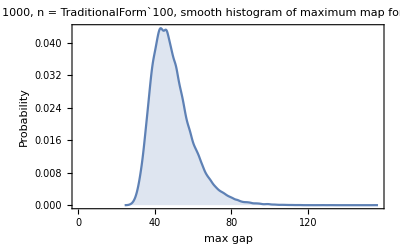

```mathematica
m=1000;
n=100;
trials = 100000;
maxGap = Table[simMaxGap[m,n],{trials}];
cgSim=SmoothHistogram[maxGap,Filling->Axis,(*PlotLegends->{"cover gap, sim"},*)
Frame->{True,True,False,False},
FrameLabel->{"max gap","Probability"},
PlotLabel->StringForm["m = ``, n = ``,
 smooth histogram of maximum map for `` trials",m,n,trials](*,PlotRange->{{-.1m,1.1 m},All}*)]
```

OrderDistribution[{BetaDistribution[1,6],6},6]

Piecewise[{{36 (1-(1-x/1000)^6)^5 (1-x/1000)^5, 0<x<1000}, {0, True}}]

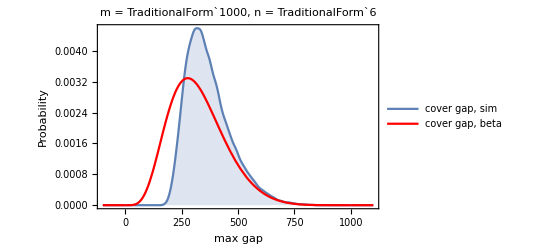

```mathematica
simMaxGap[m_,n_]:=Module[{d,ds},
(* Returns the max gap when n points are selected (without replacement) from set 1 to m
 *)
(*d=RandomSample[Range[m],n];*)
d = Join[RandomSample[Range[m],n],{0,m+1}];
ds = Sort[d];
Return[Max[Differences[ds]]]
]
m=1000;
n=6;
mD =OrderDistribution[{BetaDistribution[1,n],n},n]
PDF[mD ,x/m]
maxGap = Table[simMaxGap[m,n],{100000}];
cgSim=SmoothHistogram[maxGap,Filling->Axis,PlotLegends->{"cover gap, sim"},
Frame->{True,True,False,False},
FrameLabel->{"max gap","Probability"},
PlotLabel->StringForm["m = ``, n = ``",m,n],PlotRange->{{-.1m,1.1 m},All}];
cgBeta=Plot[PDF[mD ,x/m] 1/m,{x,-.1m,1.1m},PlotRange->All,PlotStyle->Red,ExclusionsStyle->Red,PlotLegends->{"cover gap, beta"}];
Show[cgSim,cgBeta]
```

```mathematica
Clear[m,n]
𝒟=OrderDistribution[{OrderDistribution[{DiscreteUniformDistribution[{1,m}],n},1],n},n]
PDF[𝒟,x]
```

OrderDistribution[{OrderDistribution[{DiscreteUniformDistribution[{1,m}],-2+n},1],n},n]

Piecewise[{{(1-(1-x/m)^(-2+n))^n-(1-(1+1/m-x/m)^(-2+n))^n, x≥1&&m-x>0}, {1-(1-m^(2-n))^n, m-x==0&&x≥1}, {0, x<1||m-x≤0}, {-((1-x/m)^(-2+n)-(1+1/m-x/m)^(-2+n))^n, m-x>0&&x≥1}, {-(-m^(2-n))^n, x≥1&&m-x==0}, {-(1-(1+1/m)^(-2+n))^n, True}}]

Piecewise[{{9999999999999995500000000000001199999999999999790000000000000025199999999999997900000000000000119999999999999995500000000000000099999999999999999/10000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000, x==100}, {(1-(1-x/100)^8)^10-(1-(101/100-x/100)^8)^10, 1≤x<100}, {0, True}}]

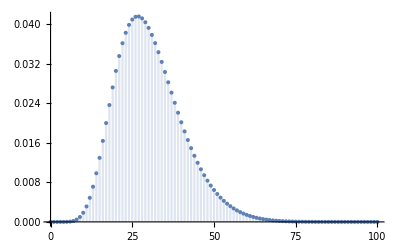

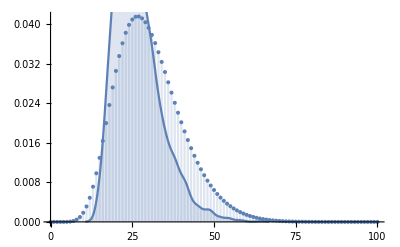

```mathematica
m = 100;
n = 10;
OrderDistribution[{OrderDistribution[{DiscreteUniformDistribution[{1,m+n}],n},1],n},n];
PDF[𝒟,x]
dicGap =DiscretePlot[PDF[𝒟,x],{x,0,m}]
simMaxGap[m_,n_]:=Max[Differences[Sort[Join[RandomSample[Range[m],n],{0,m+1}]]]];
trials = 10000;
maxGap = Table[simMaxGap[m,n],{trials}];
cgSim=SmoothHistogram[maxGap,Filling->Axis,
Frame->{True,True,False,False},
FrameLabel->{"k (Max gap)","Probability"},
PlotLabel->StringForm["m = ``, n = ``,
 smooth histogram of maximum map for `` trials",m,n,trials]];
Show[dicGap,cgSim]
```

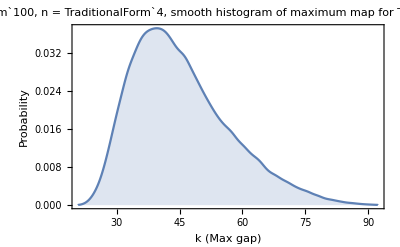

```mathematica
simMaxGap[m_,n_]:=Max[Differences[Sort[Join[RandomSample[Range[m],n],{0,m+1}]]]];
m=100;n=4;trials = 100000;
maxGap = Table[simMaxGap[m,n],{trials}];
cgSim=SmoothHistogram[maxGap,Filling->Axis,
Frame->{True,True,False,False},
FrameLabel->{"k (Max gap)","Probability"},
PlotLabel->StringForm["m = ``, n = ``,
 smooth histogram of maximum map for `` trials",m,n,trials]]
```

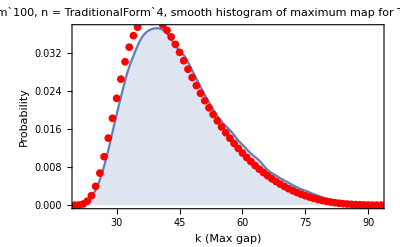

```mathematica
maxGapCDF[g_,n_,m_]:=Module[{K = Min[n+1,If[g≤ 0,n+1,Floor[(m-n)/g]]]},∑_(k=1)^K (-1)^(k-1)Binomial[n+1,k](1-k  (g+2)/(m+n+0))^n]
(*maxGapCDF[g_,n_,m_]:=Module[{K = Min[n+1,If[g≤ 0,n+1,Floor[(m-n)/g]]]},∑_(k=1)^K (-1)^(k-1)Binomial[n+1,k](1-k g/(m+1-n))^n]*)

cgAcc = ListPlot[Table[-maxGapCDF[g,n,m-n]+maxGapCDF[g-1,n,m-n],{g,0,m+1}],PlotStyle->Red];
Show[cgSim,cgAcc]
```

```mathematica
Clear[n]
Binomial[n+1,1]
```

1+n

(0
0
0
0
0
1
0)

(0 | 0 | 0 | 1/27 | 11/16 | 1
0 | 0 | 1/4 | 22/27 | 5/16 | 0
0 | 1/5 | 9/16 | 4/27 | 0 | 0
0 | 2/5 | 3/16 | 0 | 0 | 0
0 | 2/5 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

{1,1,1,1,1,1}

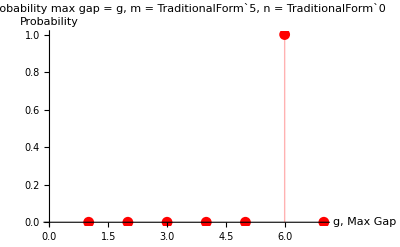

```mathematica
m=5;
n=0;
maxGapCDF[g_,n_,m_]:=Module[{K = Min[n+1,If[g≤ 0,n+1,Floor[(m-n)/g]]]},∑_(k=1)^K (-1)^(k-1)Binomial[n+1,k](1-k g/(m+1-n))^n]
d = Table[maxGapCDF[g,n,m]-maxGapCDF[g+1,n,m],{g,0,m+1}];
d2 = Table[maxGapCDF[g,n,m]-maxGapCDF[g+1,n,m],{g,0,m+1},{n,0,m}]; (*look at columns*)
d//MatrixForm
d2//MatrixForm
Total[d2,{1}]
ListPlot[d,PlotStyle->Red,Filling->Axis,AxesLabel->{"g, Max Gap","Probability"},PlotLabel->StringForm["probability max gap = g, m = ``, n = ``",m,n],PlotRange->All]
```

## Formula from http://math.stackexchange.com/questions/18938/maximum-gap-among-n-points-on-a-circle Add 1 to it, works reasonably well for large N

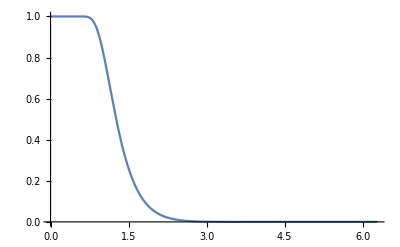

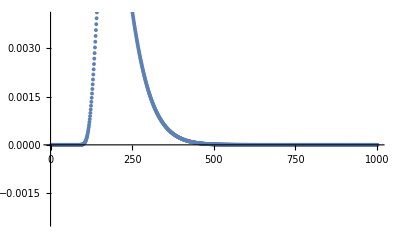

```mathematica
(*http://math.stackexchange.com/questions/18938/maximum-gap-among-n-points-on-a-circle*)
FmaxgapCircle[θ_,N_]:=Module[{K = Min[N,If[θ==0,N,(2π)/θ]]},∑_(k=1)^K (-1)^(k-1)Binomial[N,k](1-k θ/(2 π))^(N-1)]
m=1000;n=16;
Plot[FmingapCircle[θ,n],{θ,0,2π}]
cgAcc = ListPlot[Table[-(FmingapCircle[θ,n]-FmingapCircle[θ-2π/m,n]),{θ,0,2π,2π/m}]]
```

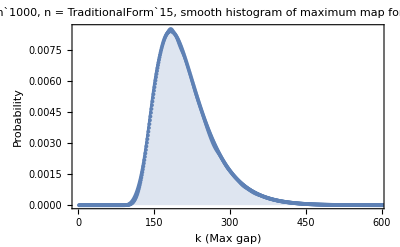

```mathematica
Show[cgSim,cgAcc]
```

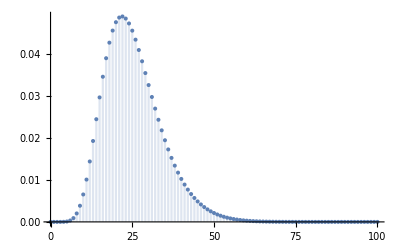

```mathematica
DiscretePlot[PDF[𝒟,x],{x,0,m}]
```

```mathematica
OrderDistribution[{DiscreteUniformDistribution[{1,10}],n},1]
```

OrderDistribution[{DiscreteUniformDistribution[{1,10}],6},1]

OrderDistribution[{OrderDistribution[{DiscreteUniformDistribution[{1,12}],2},1],6},6]

Piecewise[{{365113869407/8916100448256, x==12}, {(1-(1-x/12)^2)^6-(1-(13/12-x/12)^2)^6, 1≤x<12}, {0, True}}]

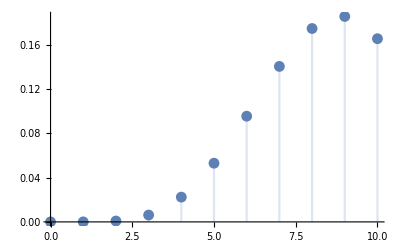

OrderDistribution[{DiscreteUniformDistribution[{1,10000}],5},5]

Piecewise[{{49990000999950001/100000000000000000000, x==10000}, {-(-1/10000+x/10000)^5+x^5/100000000000000000000, 1≤x<10000}, {0, True}}]

```mathematica
𝒟=OrderDistribution[{OrderDistribution[{DiscreteUniformDistribution[{1,12}],2},1],n},n]
PDF[𝒟,x]
Block[{n=3},DiscretePlot[PDF[𝒟,x],{x,0,10}]]
```

```mathematica
Clear[m,n]
m=100;
n=5;
discS=OrderDistribution[{Differences[RandomSample[Range[m],n]],n},n];
PDF[discS ,x]
DiscretePlot[PDF[discS ,x],{x,0,m},PlotRange->All,PlotStyle->Red,PlotLegends->{"cover gap, beta"}]
```

PDF[OrderDistribution[{{-35,-44,67,-21},5},5],x]

-Graphics-

### WHY ARE THESE DIFFERENT? Because order distribution does not sample without replacement.

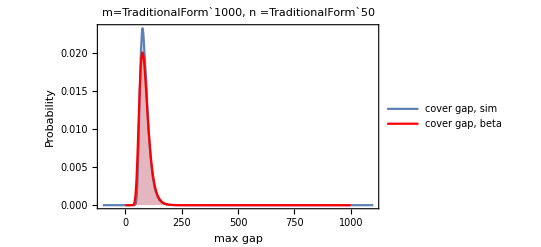

```mathematica
m=1000; (*universe of [1...m]*)
n=50;(* number of samples*)
simMaxGap[m_,n_]:=(* Returns the max gap when n points are selected (without replacement) from set 1 to m
 *)Max[Differences[Sort[Join[RandomSample[Range[m],n],{0,m+1}]]]];

maxGap = Table[simMaxGap[m,n],{100000}];
cgSim=SmoothHistogram[maxGap,Filling->Axis,PlotLegends->{"cover gap, sim"},
Frame->{True,True,False,False},
FrameLabel->{"max gap","Probability"},
PlotLabel->StringForm["m=``, n =``",m,n],PlotRange->{{-.1m,1.1 m},All}];
discS=OrderDistribution[{OrderDistribution[{DiscreteUniformDistribution[{1,m}],n},1],n},n];
PDF[discS ,x];
cgDisc=DiscretePlot[PDF[discS ,x],{x,0,m},PlotRange->All,PlotStyle->Red,PlotLegends->{"cover gap, beta"}];
Show[cgSim,cgDisc]
```

### http://math.stackexchange.com/questions/66430/what-is-the-distribution-of-gaps the two versions disagree

```mathematica
gapDist[m_,n_,i_,k_]:=Module[{maxGap = Min[n,If[i>1,Floor[(m-n)/(i-1)],n]]},
(*http://math.stackexchange.com/questions/66430/what-is-the-distribution-of-gaps*)
(* Randomly select n numbers from the universe {1,2…,m} with or without replacement,and sort the numbers in ascending order.We can get a list of number {a1,a2,…,an},and then we can get the difference between two consecutive numbers and get the gap list:{a1,a2−a1,…,an−an−1}
So my question is:what is the distribution of the gaps.
P(Ai=k)=P(m,n,i,k)
*)
If[ 1≤n≤m && 1≤i≤m+1-n&& 0≤k≤ maxGap,
1/Binomial[m,n]∑_(j=k)^maxGap (-1)^(j-k)Binomial[j,k]   Binomial[n,j] Binomial[m-i*j,n-j] ,0]]
```

```mathematica
Table[N[gapDist[10,n,1,2]],{n,1,9}]
```

{0.,0.0222222,0.175,0.428571,0.396825,0.0714286,0.,0.,0.}

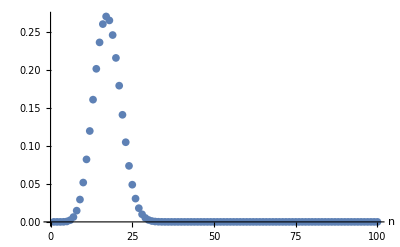

```mathematica
m = 100;
ListPlot[Table[N[gapDist[m,n,1,3]],{n,1,m}],PlotRange->All,AxesLabel->{"n"}]
```

```mathematica
gapkgapsSize1[m_,n_,k_]:=(*1 to m objects, select n, probability of k gaps of size 1?*)(Binomial[n+1,k]Binomial[m-(n+1),n-k])/Binomial[m,n]
```

```mathematica
Table[N[gapkgapsSize1[10,n,2]],{n,1,9}]
```

{0.,0.0666667,0.3,0.47619,0.238095,0.,0.,0.,0.}

```mathematica
N[80*365/3000]
```

9.73333

## Compare to solution given on stack exchange

```mathematica
simMaxGap[m_,n_]:=Max[Differences[Sort[Join[RandomSample[Range[m],n],{0,m+1}]]]];
trials = 100;
gridsize =64;
maxGapmn = ConstantArray[NaN,{gridsize,gridsize}];
 Table[maxGapmn⟦n,m⟧=Mean[ Table[simMaxGap[m,n],{trials}]],{m,1,gridsize},{n,1, m}] ;
```

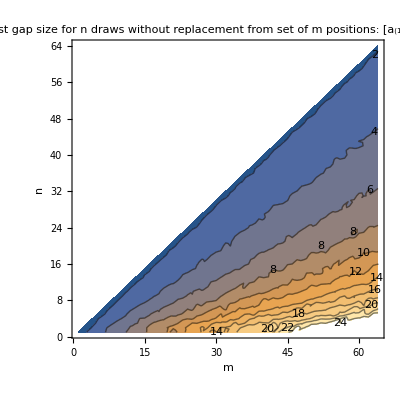

```mathematica
ListContourPlot[maxGapmn,FrameLabel->{"m","n"},PlotLabel->"E(G_(n, m))
Expected largest gap size for n draws without replacement
 from set of m positions: [a_(1)-0, a_(2)-a_(1),..., a_(n)-a_(n - 1), m+1-a_(n)]",Contours->2Range[1,32],ContourLabels->All]
```

```mathematica
N[maxGapmn]
```

## Example from stack exchange (dynamic program, slow)

```mathematica
Binomial[0,3]
```

0

```mathematica
gapf[0,2,3]
```

1

```mathematica
gapf[g_,n_,m_]:=(*Probability that the minimum,Subscript[a, (1)],equals g;that is,the sample consists of g and an n−1-subset of {g+1,g+2,…,m}.*)
If[n>m ||g>m ,0,Binomial[m-g,n-1]/Binomial[m,n]]
gapQ[g_,n_,m_]:=(*
Adding f(k,n,m) for all possible values of k greater than g yields the survival function*)If[g≥ m || n>m,0,((m-g)Binomial[m-g-1,n-1])/(n Binomial[m,n])];
gapP[g_,1,m_]:=If[g≥ m,0, (m-g)/m];
gapP[g_Integer,n_,m_]:=gapQ[g,n,m]+∑_(k=1)^g gapf[k,n,m]gapP[g,n-1,m-k]
```

```mathematica
rg = 64;
gv=rg+1;nv =rg;mv =rg;
gapf[g_,n_,m_]:=(*Probability that the minimum,Subscript[a, (1)],equals g;that is,the sample consists of g and an n−1-subset of {g+1,g+2,…,m}.*)
If[n>m ||g>m ,0,Binomial[m-g,n-1]/Binomial[m,n]]
gapQ[g_,n_,m_]:=(*
Adding f(k,n,m) for all possible values of k greater than g yields the survival function*)If[g≥ m || n>m,0,((m-g)Binomial[m-g-1,n-1])/(n Binomial[m,n])];
Gnm =ConstantArray[ 0,{gv+1,nv,mv}];
(*fill in the first row*)
Table[Gnm⟦g+1,1,;;⟧= Table[If[g≥ m,0, (m-g)/m],{m,Range[mv]}],{g,Range[0,gv]}];
(*fill in successive rows*)
Table[Gnm⟦g+1,n,;;⟧= Table[gapQ[g,n,m]+∑_(k=1)^g (gapf[k,n,m]Gnm⟦g+1,n-1,m-k⟧),
{m,Range[mv]}];,{g,Range[0,gv]},{n,Range[2,nv]}];
```

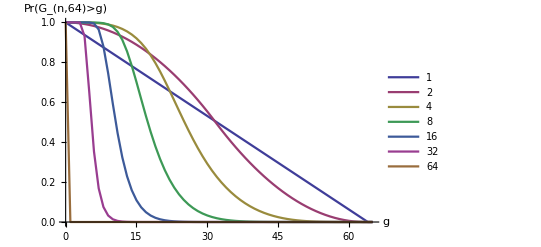

```mathematica
nvs = {1,2,4,8,16,32,64};
ListLinePlot[Table[Gnm⟦;;,n,64⟧,{n,nvs}],PlotLegends->nvs,PlotStyle->ColorData[1,"ColorList"],(*PlotStyle->Thick,*)DataRange->{0,65},AxesLabel->{"g","Pr(G_(n,64)>g)"}]
```

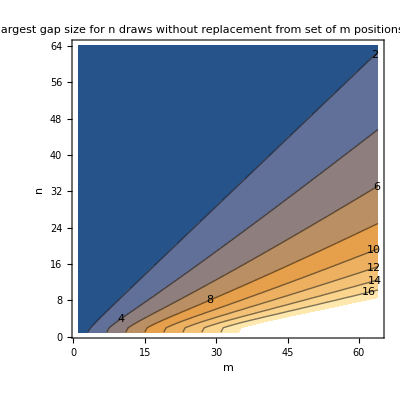

```mathematica
ListContourPlot[Total[Gnm,{1}],Contours->2Range[32],ContourLabels->True,FrameLabel->{"m","n"},PlotLabel->"E(G_(n, m))
Expected largest gap size for n draws without replacement
 from set of m positions: [a_(1)-0, a_(2)-a_(1),..., a_(n)-a_(n - 1)]"]
```

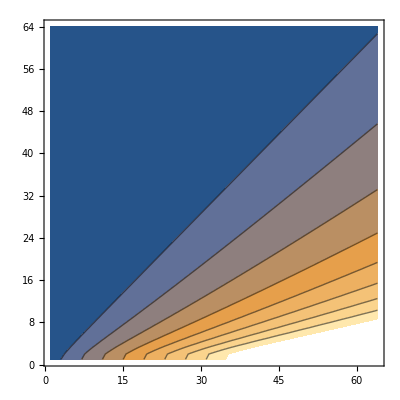

```mathematica
expGnm = Table[  ∑_(g=0)^(m-n+1)  Gnm⟦g+1,n,m⟧,{n,Range[nv]},{m,Range[mv]}];
ListContourPlot[expGnm,Contours->2Range[32]]
```

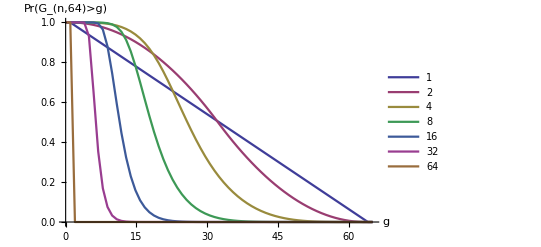

```mathematica
ListLinePlot[Table[Prepend[Gnm⟦;;,n,64⟧,1],{n,nvs}],PlotLegends->nvs,PlotStyle->ColorData[1,"ColorList"],PlotStyle->Thick,DataRange->{0,65},AxesLabel->{"g","Pr(G_(n,64)>g)"}]
```

```mathematica
(*http://mathematica.stackexchange.com/questions/53/how-can-i-implement-dynamic-programming-for-a-function-with-more-than-one-argume*)
CharlierC[0,a_,x_]:=1;
CharlierC[1,a_,x_]:=x-a;
CharlierC[n_Integer,a_,x_]:=Module[{al,xl},Set@@Hold[CharlierC[n,al_,xl_],Expand[(xl-al-n+1) CharlierC[n-1,al,xl]-al (n-1) CharlierC[n-2,al,xl]]];
CharlierC[n,a,x]];
```

$Aborted